```mathematica
ClearAll["Global`*"]
data=Import[FileNameJoin[{NotebookDirectory[],"histogram.json"}]];
Column[data[[;;,1]]]
```

where_divide
bin_width
count
cumulative
diff
interval
mid_interval

```mathematica
counts="count"/.data;
midinterval="mid_interval"/.data;
wheredivide="where_divide"/.data;
Manipulate[BarChart[counts[[n]],
ChartLabels->midinterval[[n]],
PlotLabel->wheredivide[[n]],
ChartStyle->(If[#≥wheredivide[[n]],Red,Blue]&/@midinterval[[n]])],
{n,1,Length[counts],1}]
```

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json

Part::partd: 部分指定/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json⟦1⟧の長さはオブジェクトの深さを超えています．

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json⟦1⟧

ReplaceAll::reps: {/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

count/./Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json

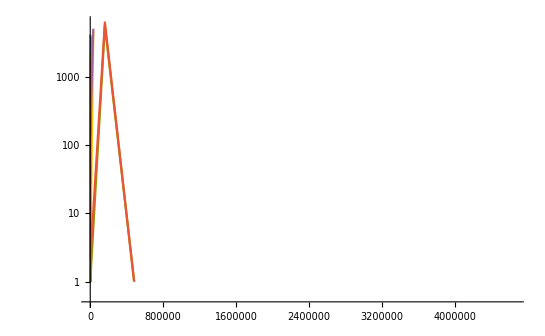

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

BarChart::nonopt: BarChart[size0/.$Failed,ChartLabels→mid_interval0/.$Failed]における1の位置より後方にオプションが想定されます（ChartLabels→mid_interval0/.$Failedの代りに）．オプションは規則あるいは規則のリストでなければなりません．

BarChart::ldata: size0は有効なデータ集合でもデータ集合のリストでもありません．

ReplaceAll::reps: {/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

BarChart::nonopt: BarChart[size0/./Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json,ChartLabels→mid_interval0/./Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json]における1の位置より後方にオプションが想定されます（ChartLabels→mid_interval0/./Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.jsonの代りに）．オプションは規則あるいは規則のリストでなければなりません．

ReplaceAll::reps: {/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

BarChart::nonopt: BarChart[size0/./Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json,ChartLabels→mid_interval0/./Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json]における1の位置より後方にオプションが想定されます（ChartLabels→mid_interval0/./Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.jsonの代りに）．オプションは規則あるいは規則のリストでなければなりません．

ReplaceAll::reps: {/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

BarChart::nonopt: BarChart[size0/./Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json,ChartLabels→mid_interval0/./Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.json]における1の位置より後方にオプションが想定されます（ChartLabels→mid_interval0/./Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_remesh/histogram.jsonの代りに）．オプションは規則あるいは規則のリストでなければなりません．

BarChart::ldata: size0は有効なデータ集合でもデータ集合のリストでもありません．

```mathematica
file=FileNameJoin[{NotebookDirectory[],"historgram.json"}];
data=Import[file];
data[[;;,1]];

maxN=100;

(*Bar Chart Plot*)
Manipulate[n=ToString[m];
BarChart[("size"<>n)/. data,ChartLabels->("mid_interval"<>n)/. data],{m,0,maxN,10}]

(*Logarithmic ListPlot*)
ListLogPlot[Table[n=ToString[m];
Transpose@{("mid_interval"<>n)/. data,("size"<>n)/. data},{m,0,maxN,10}],Joined->True,PlotRange->Full]
```